# Create Ontology Graph

## Import CloudObjects

Import the data that was exported to the cloud from this notebook.

```mathematica
siteDirectory=CloudObject["FoodOntologyGraph"];
```

```mathematica
entityTypeToMetaDataWithNodes=Import[FileNameJoin[{siteDirectory,"EdgeData.m"}]];
allNodesProcessed=Import[FileNameJoin[{siteDirectory,"NodeData.m"}]];
allNodesGrouped=Import[FileNameJoin[{siteDirectory,"GroupedNodes.m"}]];
```

## Create basic graph

Create graph edges from the data, keeping all metadata available as edge properties:

```mathematica
ClearAll[createEdge];
createEdge[a_Association,{Key[entityType_],Key[property_EntityProperty]}]:=Property[DirectedEdge[entityType,a["Node"]],Normal[a]];
allEdges=Flatten@Values[Values/@MapIndexed[createEdge,entityTypeToMetaDataWithNodes,{2}]];
allEdges=DeleteCases[allEdges,Property[DirectedEdge[_,_Missing],___]];
allEdges//Length
```

892

The basic graph is a bit messy:

```mathematica
basicGraph=Graph[allNodesProcessed,allEdges,GraphLayout->"SpringEmbedding"]
```

-Graphics-

## Remove or hide redundant edges

To clean up the graph, delete any “Name” property edges, as they all go to the “String” data type:

```mathematica
allEdgesSimpler1=DeleteCases[allEdges,Property[DirectedEdge[_,"String"],{___,"Label"->"name"|"alternative names",___}]];
allEdgesSimpler1//Length
```

835

The graph is much cleaner:

```mathematica
simplerGraph1=Graph[allNodesProcessed,allEdgesSimpler1,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

Make any “foods” or “strict foods” properties transparent, as all food attribute entities have these two properties.
Keeping the properties around helps keep the nice circular shape which will be useful later.

```mathematica
allEdgesSimpler2=allEdgesSimpler1/.Property[edge:DirectedEdge[_,"Food"],props:{___,"Label"->"foods"|"strict foods",___}]:>Property[edge,Append[props,EdgeStyle->Transparent]];
```

```mathematica
allEdgesSimpler2//VertexList//Length
```

82

The graph is a bit more simple:

```mathematica
simplerGraph2=Graph[allNodesProcessed,allEdgesSimpler2,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

To avoid cluttering the graph, remove edges that connect the special food entity types to another category:

```mathematica
simplerGraph3=EdgeDelete[simplerGraph2,DirectedEdge["LanguaLTerm"|"PLUCode"|"FoodIngredient"|"Nutrient"|"DietaryRestriction",_]]
```

-Graphics-

Doing this disconnects a few entity types from the rest of the graph, so they should be removed:

```mathematica
nodesNoLongerNeeded=Complement[VertexList[simplerGraph3],Flatten[KCoreComponents[simplerGraph3,1]]]
```

{DateObject,ICDNine,ICDTen}

```mathematica
allNodesGroupedFinal=DeleteCases[#,Alternatives@@nodesNoLongerNeeded]&/@allNodesGrouped;
```

```mathematica
simplerGraph=VertexDelete[simplerGraph3,nodesNoLongerNeeded]
```

-Graphics-

## Build Node index

Go through the nodes and assign them an index:

```mathematica
simplerGraphFinal=simplerGraph;
MapIndexed[(simplerGraphFinal=SetProperty[{simplerGraphFinal,#1},"Index"->First[#2]])&,VertexList[simplerGraph]];
```

## Group nodes into Communities, add styling

This uses CommunityGraphPlot to create a visually appealing and meaningful organization of the ontology graph data.

### Definitions

```mathematica
ClearAll[decamel];
decamel[s_String]:=StringReplace[s,a_?LowerCaseQ~~b_?UpperCaseQ:>a<>" "<>b];
decamel[x_]:=x;

ClearAll[makeOntologyGraph];
makeOntologyGraph[g_Graph,labelToNodeGroup_Association,size_:Medium]:=Module[
{labelFontSize,labelPadding,nodeGroupings,styledGraph,communityGraphImageSize},

labelFontSize=Replace[size,{Large->50,Medium|_->18}];
labelPadding=Replace[size,{Large->"\n\n",Medium|_->"\n"}];
nodeGroupings=KeyValueMap[Labeled[#2,Style[#1<>labelPadding,labelFontSize,FontFamily->"Source Sans Pro",#2[[2]],Bold],Above]&,labelToNodeGroup];

communityGraphImageSize=Replace[size,{Large->4000,Medium|_->850}];

styledGraph=styleGraph[g,size];

CommunityGraphPlot[
styledGraph,
nodeGroupings,
Method->"Hierarchical",
CommunityBoundaryStyle->None,
ImageSize->communityGraphImageSize
]

];

ClearAll[formatEdgeLabelMetadata];
formatEdgeLabelMetadata[g_Graph,edge_,{}]:=None;
formatEdgeLabelMetadata[g_Graph,edge_,props_]:=Module[
{data},
data=AssociationMap[Function[{prop},PropertyValue[{g,edge},prop]],props];
(* TODO: Take care of what should live here before now? *)
(* TODO: Remove stupid things, like "Unit"->None *)
data=DeleteMissing[data]//KeyDrop[{"Node","OutputType",EdgeShapeFunction,EdgeStyle}];
data=KeyValueMap[{decamel[#1],#2}&,data];
data=DeleteCases[data,{"Unit",None}];
If[Length[data]>1,
Grid[data,Background->{{LightGray},Automatic},Frame->All],
None
]
];

(* Styles the graph according to the size for optimal viewing *)
ClearAll[styleGraph];
styleGraph[g_Graph,size_]:=Module[
{vertexLabels,vertexSizes,edgeLabels,nodeLabelProperty,labelSimplificiationRules,arrowheadSize},

nodeLabelProperty=Replace[size,{Large->"Label",Medium|_->"Index"}];
arrowheadSize=Replace[size,{Large->0.01,Medium|_->0.02}];

labelSimplificiationRules={
"nutritional supplement"->"nutritional\nsupplement",
"nutritional supplement not added"->"nutritional\nsupplement\nnot added",
"product lookup codes"->"product\nlookup\ncodes"
};

vertexLabels=Rule[
#,
Placed[
{
Style[Replace[PropertyValue[{g,#},nodeLabelProperty],labelSimplificiationRules],fontColor,Bold,FontFamily->"Source Sans Pro"],
(* TODO: Construct grids for each earlier than this? *)
Replace[PropertyValue[{g,#},"Label"],{Except[_String]:>Echo[#,"No Label:",InputForm],s_String:>Capitalize[s]}]
},
{Center,Tooltip}
]
]&/@VertexList[g];

vertexSizes=Rule[#,Replace[PropertyValue[{g,#},"Group"],{"MajorFoodEntityType"->{"Scaled",0.03},_->Automatic}]]&/@VertexList[g];

edgeLabels=With[
{props=Replace[PropertyList[{g,#}],Except[_List]->{}]},
Rule[
#,
If[MatchQ[PropertyValue[{g,#},EdgeStyle],Transparent],
None,
Placed[formatEdgeLabelMetadata[g,#,props],Tooltip]
]
]
]&/@EdgeList[g];

SetProperty[g,
{
EdgeStyle->Directive[Opacity[0.35],Arrowheads[List@{arrowheadSize,0.9}]],
VertexLabels->vertexLabels,
VertexSize->vertexSizes,
EdgeLabels->edgeLabels
}
]
];

(* Create the final grouping of the different types *)
foodColor=RGBColor[1., 0.41, 0.];
otherColor=RGBColor[0.3137254901960784, 0.5176470588235293, 0.7137254901960784];
basicColor=RGBColor[0.42, 0.69, 0.18];
quantityColor=RGBColor[0.46, 0.25, 0.58];
specialColor=RGBColor[0.8509803921568627, 0.06274509803921569, 0.0784313725490196];
fontColor=White;

nodeGroupingsFinal=<|
"Food Entity Types"->Style[Flatten[Lookup[#,{"MajorFoodEntityTypes","OtherFoodEntityTypes"}]],foodColor],
"Other Entity Types"->Style[Flatten[Lookup[#,{"OtherEntityTypes"}]],otherColor],
"Basic Data Types"->Style[Flatten[Lookup[#,{"BasicDataTypes"}]],basicColor],
"Physical Quantities"->Style[Flatten[Lookup[#,{"Quantities"}]],quantityColor],
"Special Food Entity Types"->Style[Flatten[Lookup[#,{"SpecialFoodEntityTypes"}]],specialColor]
|>&[allNodesGroupedFinal];
```

### Medium images

This will be used on the home page, showing just the index number for each node:

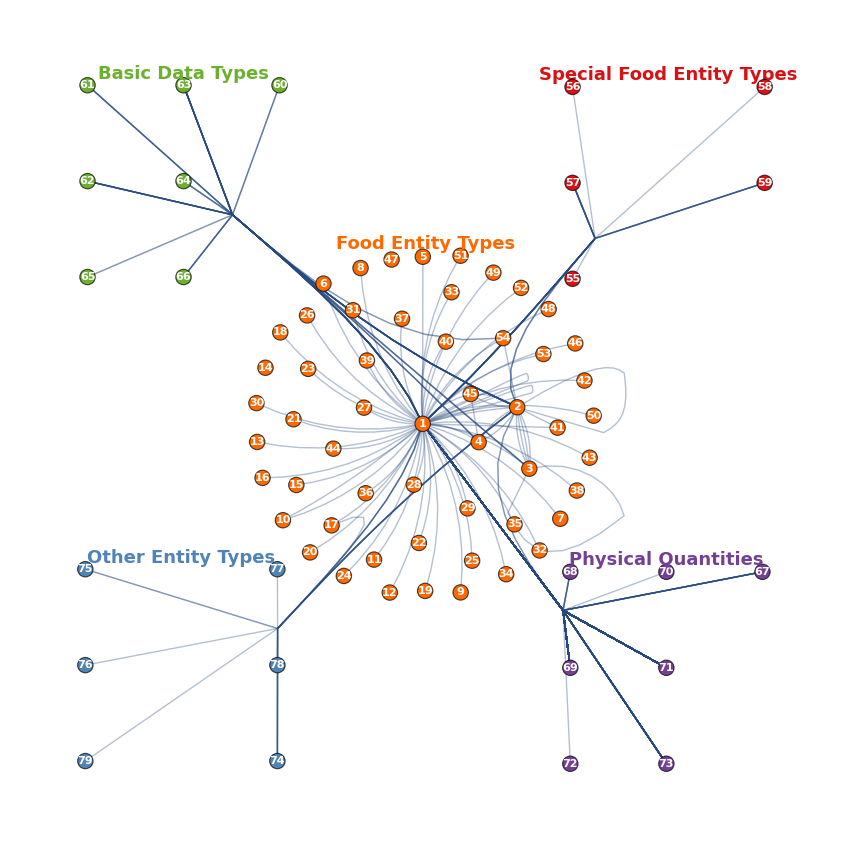

```mathematica
mediumOntologyGraph=makeOntologyGraph[simplerGraphFinal,nodeGroupingsFinal]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["OntologyGraph_NoLegend_Medium.png",mediumOntologyGraph]
```

OntologyGraph_NoLegend_Medium.png

```mathematica
SetDirectory[NotebookDirectory[]];
Export["OntologyGraphGraph_NoLegend_Medium.PDF",mediumOntologyGraph]
```

OntologyGraphGraph_NoLegend_Medium.PDF

### Large Images

This will be used on the website to zoom in further and see the full label on each node:

```mathematica
largeOntologyGraph=makeOntologyGraph[simplerGraph,nodeGroupingsFinal,Large];
```

#### PDF

A PDF provides a way to see the ontology graph as a vector image:

```mathematica
SetDirectory[NotebookDirectory[]];
Export["OntologyGraph_NoLegend_Large.pdf",largeOntologyGraph]
```

OntologyGraph_NoLegend_Large.pdf

#### Large PNG

```mathematica
SetDirectory[NotebookDirectory[]];
Export["OntologyGraph_NoLegend_Large.png",largeOntologyGraph]
```

OntologyGraph_NoLegend_Large.png

#### SVG

```mathematica
SetDirectory[NotebookDirectory[]];
Export["largeOntologyGraph.svg",largeOntologyGraph]
```

largeOntologyGraph.svg

### HTML Image Map

An HTML Image Map allows for adding hyperlinks and tooltips to parts of an image for use in a browser.

#### Function to create an EmbeddedHTML object

```mathematica
ClearAll[createImageMap];
Options[createImageMap]={"LocalDirectory"->Automatic,Permissions->Automatic};
createImageMap::usage="createImageMap[dir_CloudObject, g_Graphics] creates an EmbeddedHTML object with an image map (image stored in dir) for the given graphics object.";
createImageMap::invalid="Check that the CloudObject `` is a directory (or doesn't exist), or that you are using a Graphics object.";
createImageMap[dir_CloudObject/;(DirectoryQ[dir]||Not@FileExistsQ[dir]),g_Graphics,OptionsPattern[]]:=Module[
{localDirectory,outputFile,html,id,imageCloudObject,permissions},

localDirectory=OptionValue["LocalDirectory"];

localDirectory=If[MatchQ[localDirectory,_String],
CreateDirectory[localDirectory],
CreateDirectory[]
];
SetDirectory[localDirectory];

(* Create a random ID to avoid collisions *)
id=CreateUUID["map-"];

(* Exporting to HTML makes an image map for Annotation[_, url_, "Hyperlink"] objects *)
outputFile=Export["Output.html",g];

(* Import the HTML code to pull out the image tag and its map *)
html=Import[outputFile,"Source"];
html=First@StringCases[html,"<p class=\"Output\">"~~imageAndMap__~~"</p>":>StringTrim[imageAndMap],1];

(* Copy the image file to the cloud in the given directory *)
(* TODO: Support PNG files? *)
imageCloudObject=CopyFile["HTMLFiles/Output_1.gif",FileNameJoin[{dir,id<>".gif"}]];

permissions=OptionValue[Permissions];
If[permissions=!=Automatic,
SetOptions[imageCloudObject,Permissions->permissions];
];

(* Update the HTML code to point to the new image *)
html=StringReplace[html,"\"HTMLFiles/Output_1.gif\"":>StringTemplate["\"``\""][First@imageCloudObject]];

(* Change the map's name to use the new ID to avoid collisions if multiple are used on one page *)
html=StringReplace[html,"map_1"->id];

ResetDirectory[];
EmbeddedHTML[html]
];
createImageMap[dir_,rest___]:=(Message[createImageMap::invalid,dir];$Failed);
```

#### Create image map

Remove tooltips on the edges for simplicity

```mathematica
mediumOntologyGraphSimplifiedTooltips=mediumOntologyGraph/.Tooltip[a_Arrow,___]:>a;
```

```mathematica
imageMap=createImageMap[
FileNameJoin[{siteDirectory,"ImageMaps"}],
mediumOntologyGraphSimplifiedTooltips,
Permissions->"Public"
];
```

$CharacterEncoding::utf8: The byte sequence {233,109} could not be interpreted as a character in the UTF-8 character encoding.

Export to the cloud for later use:

```mathematica
SetDirectory[NotebookDirectory[]];
Quiet@CreateDirectory["ImageMaps"];
Export["ImageMaps/imageMap.m",imageMap,"Package"]
```

ImageMaps/imageMap.m

At this point, the core of the ontology graph is done! But creating a legend and an edge table will improve readability.

## Add a legend (simple)

Gather all of the data available:

```mathematica
nodeToLegendData=AssociationMap[
Function[{node},
AssociationMap[
PropertyValue[{simplerGraphFinal,node},#]&,
PropertyList[{simplerGraphFinal,node}]
]
],
VertexList[simplerGraph]
];
```

Build a legend using the colors used in the plot:

```mathematica
groupToColor=<|
"BasicDataTypes"->basicColor,
"MajorFoodEntityTypes"->foodColor,
"OtherEntityTypes"-> otherColor,
"OtherFoodEntityTypes"->foodColor,
"Quantities"->quantityColor,
"SpecialFoodEntityTypes"->specialColor
|>;
```

```mathematica
legendData={#Index,#Label,groupToColor[#Group]}&/@Values[nodeToLegendData];
```

```mathematica
ClearAll[formatLegendColumn];
formatLegendColumn[legendData_]:=Module[
{gridData,backgroundSpec,sowTag},
{gridData,{backgroundSpec}}=Reap[
MapIndexed[
Replace[{##},{{index_,label_,groupColor_},{position_Integer}}:>(Sow[{position,2}->groupColor,sowTag];{index,Style[label,fontColor]})]&,
legendData
],
sowTag
];
Style[Grid[gridData,Background->{None,None,backgroundSpec},Alignment->{{Right,Left}},Dividers->{{1->True,-1->True},All}],FontFamily->"Source Sans Pro"]
];
```

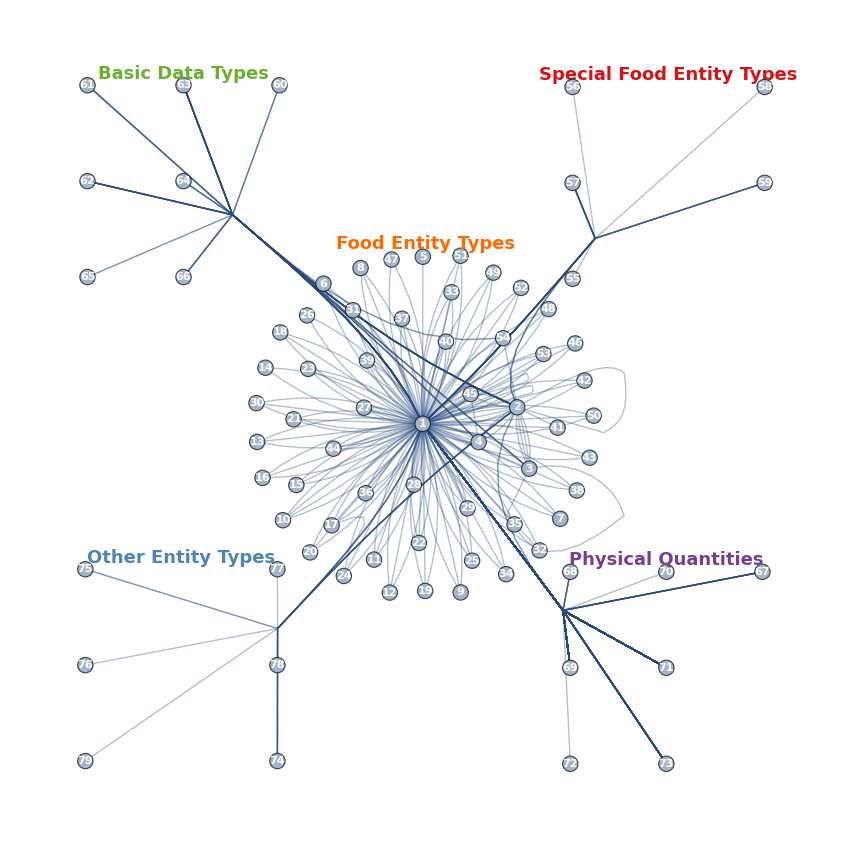
-Graphics-1 | food
2 | food type
3 | food type group
4 | basic food group
5 | cooking method
6 | age
7 | alcohol label
8 | beef grade
9 | bone content
10 | brand name
11 | caffeine label
12 | calorie label
13 | composition
14 | concentration
15 | crust type
16 | culture
17 | data source
18 | fat label
19 | fat type
20 | fiber label
21 | flavor
22 | geometry type
23 | intended use
24 | iron label
25 | location
26 | manufacturer
27 | meat cut
28 | meat quality
29 | moisture level
30 | nutritional supplement
31 | nutritional supplement not added
32 | packaging
33 | part
34 | patty count
35 | peeling type
36 | preparation
37 | processing type
38 | seafood variety
39 | seed content
40 | serving type | 41 | shape
42 | food size
43 | skin content
44 | sodium label
45 | food state
46 | serving type
47 | sub brand name
48 | sugar label
49 | sugar type
50 | texture
51 | trimming level
52 | food variety
53 | vegetable part
54 | USDA food group
55 | LanguaL term
56 | product lookup code
57 | nutrient
58 | food ingredient
59 | dietary restriction
60 | Boolean
61 | Number
62 | String
63 | Association
64 | Graphics
65 | Image
66 | Entity Property
67 | energy
68 | energy per mass
69 | mass
70 | mass density
71 | mass ratio
72 | volume
73 | quantity
74 | set of colors
75 | country
76 | language
77 | Pokémon
78 | solid
79 | transparency

```mathematica
mediumImageWithLegend=Row[{mediumOntologyGraph,Style[#,16]&@Grid[List@(formatLegendColumn/@Partition[legendData,40,40,1,{}]),Frame->All,FrameStyle->Thick,Alignment->Top]}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["OntologyGraph_WithLegend_Medium_TwoColumn.pdf",mediumImageWithLegend]
```

OntologyGraph_WithLegend_Medium_TwoColumn.pdf

## Create an edge table

This allows for seeing the edges more clearly in a grid format.

### Gather edges into groups

```mathematica
nodeGroupingsSimpler=nodeGroupingsFinal/.Style[x_,___]:>x;
nodeToGroup=GroupBy[Flatten[KeyValueMap[Thread[Rule[##]]&,nodeGroupingsSimpler]],Last->First,First];
nodeToGroup[[;;3]]
```

<|Food→Food Entity Types,FoodType→Food Entity Types,FoodTypeGroup→Food Entity Types|>

Group the edges by their starting and ending node groups:

```mathematica
groupedEdges=GroupBy[EdgeList[simplerGraphFinal],Map[nodeToGroup],DeleteDuplicates];
```

```mathematica
groupedEdges//Map[Length]//ReverseSort//KeyValueMap[List]//Grid[#,Frame->All]&
```

Food Entity Types->Food Entity Types | 114
Food Entity Types->Basic Data Types | 19
Food Entity Types->Other Entity Types | 8
Food Entity Types->Physical Quantities | 8
Food Entity Types->Special Food Entity Types | 6

Find a list of all edges with complete metadata, given their starting and ending nodes:

```mathematica
basicEdgeToFullEdgeMetadata=GroupBy[
allEdgesSimpler2,
First->(Append[Last[#],"SourceNode"->#[[1,1]]]&),
Map[Association]
];
Total[Length/@basicEdgeToFullEdgeMetadata]

(* Remove transparent edges *)
basicEdgeToFullEdgeMetadata=Select[KeyFreeQ[EdgeStyle]]/@basicEdgeToFullEdgeMetadata;
Total[Length/@%]
```

835

732

Gather the metadata according to the edges between the major groups:

```mathematica
bigGroupEdgesToMetadata=Flatten/@(Map[basicEdgeToFullEdgeMetadata]/@groupedEdges);
```

### Definitions

```mathematica
(* This is tuned for Source Sans Pro *)
ClearAll[numberCircle];
numberCircle[n_Integer,rest___]/;n<10:=numberCircle[(*"  "<>ToString[n]<>"  "*)"  "<>ToString[n]<>"  ",rest];
numberCircle[n_Integer,rest___]:=numberCircle[" "<>ToString[n]<>" ",rest];
numberCircle[s_String,background_:Automatic]:=Highlighted[Style[s,fontColor,Bold,FontFamily->"Source Sans Pro"],Background->background,RoundingRadius->Scaled[0.25],Frame->True,FrameStyle->Directive[Black,Thick]];
numberCircle[s_String,background_,tooltip_]:=Tooltip[numberCircle[s,background],tooltip];
Row[Style[numberCircle[#,Green,"TEST"],35]&/@{5,15},Spacer[1]]
```

5   15

```mathematica
majorGroupToColor=Last/@nodeGroupingsFinal
```

<|Food Entity Types→RGBColor[1., 0.41, 0.],Other Entity Types→RGBColor[0.3137254901960784, 0.5176470588235293, 0.7137254901960784],Basic Data Types→RGBColor[0.42, 0.69, 0.18],Physical Quantities→RGBColor[0.46, 0.25, 0.58],Special Food Entity Types→RGBColor[0.8509803921568627, 0.06274509803921569, 0.0784313725490196]|>

```mathematica
ClearAll[nodeToLabel];
nodeToLabel[node_]:=PropertyValue[{simplerGraphFinal,node},"Label"];

ClearAll[nodeToIndex];
nodeToIndex[node_]:=PropertyValue[{simplerGraphFinal,node},"Index"];

ClearAll[edgeToMetadata];
edgeToMetadata[edge_]:=formatEdgeLabelMetadata[simplerGraphFinal,edge,DeleteCases[Replace[PropertyList[{simplerGraphFinal,edge}],Except[_List]->{}], "Label"]];
```

```mathematica
nodeToNumberedCircle=MapIndexed[numberCircle[nodeToIndex[#2[[1,1]]],#1,nodeToLabel[#2[[1,1]]]]&,majorGroupToColor/@nodeToGroup]
```

<|Food→  1  ,FoodType→  2  ,FoodTypeGroup→  3  ,BasicFoodGroup→  4  ,CookingMethod→  5  ,FoodAge→  6  ,FoodAlcoholLabel→  7  ,FoodBeefGrade→  8  ,FoodBoneContent→  9  ,FoodBrandName→ 10 ,FoodCaffeineLabel→ 11 ,FoodCalorieLabel→ 12 ,FoodComposition→ 13 ,FoodConcentration→ 14 ,FoodCrustType→ 15 ,FoodCulture→ 16 ,FoodDataSource→ 17 ,FoodFatLabel→ 18 ,FoodFatType→ 19 ,FoodFiberLabel→ 20 ,FoodFlavor→ 21 ,FoodGeometryType→ 22 ,FoodIntendedUse→ 23 ,FoodIronLabel→ 24 ,FoodLocation→ 25 ,FoodManufacturer→ 26 ,FoodMeatCut→ 27 ,FoodMeatQuality→ 28 ,FoodMoistureLevel→ 29 ,FoodNutritionalSupplement→ 30 ,FoodNutritionalSupplementNotAdded→ 31 ,FoodPackaging→ 32 ,FoodPart→ 33 ,FoodPattyCount→ 34 ,FoodPeelingType→ 35 ,FoodPreparation→ 36 ,FoodProcessingType→ 37 ,FoodSeafoodVariety→ 38 ,FoodSeedContent→ 39 ,FoodServingType→ 40 ,FoodShape→ 41 ,FoodSize→ 42 ,FoodSkinContent→ 43 ,FoodSodiumLabel→ 44 ,FoodState→ 45 ,FoodStorageType→ 46 ,FoodSubBrandName→ 47 ,FoodSugarLabel→ 48 ,FoodSugarType→ 49 ,FoodTexture→ 50 ,FoodTrimmingLevel→ 51 ,FoodVariety→ 52 ,FoodVegetablePart→ 53 ,USDAFoodGroup→ 54 ,ColorSet→ 74 ,Country→ 75 ,Language→ 76 ,Pokemon→ 77 ,Solid→ 78 ,Transparency→ 79 ,Boolean→ 60 ,Number→ 61 ,String→ 62 ,Association→ 63 ,Graphics→ 64 ,Image→ 65 ,EntityProperty→ 66 ,Energy Energy→ 67 ,EnergyPerMass EnergyPerMass→ 68 ,Mass Mass→ 69 ,MassDensity MassDensity→ 70 ,MassRatio MassRatio→ 71 ,Volume Volume→ 72 ,Quantity→ 73 ,LanguaLTerm→ 55 ,PLUCode→ 56 ,Nutrient→ 57 ,FoodIngredient→ 58 ,DietaryRestriction→ 59 |>

```mathematica
ClearAll[metadataToNumberRow];
metadataToNumberRow[propertyLabel_String,metadata_Association]:=Module[
{
lhsNodes=Lookup[metadata,"SourceNode"],
rhsNode=First@Lookup[metadata,"Node"]
},
{
Row[nodeToNumberedCircle/@SortBy[lhsNodes,nodeToIndex],Spacer[0.5]],
Replace[Tooltip[propertyLabel,edgeToMetadata[DirectedEdge[First[lhsNodes],rhsNode]]],Tooltip[x_,None]:>x],
nodeToNumberedCircle@rhsNode
}
];
```

```mathematica
ClearAll[metadataRowsToGrid];
metadataRowsToGrid[label_,rows:{__List}]:=Style[
Grid[
Join[
{
{Style[label,18,Bold,Lookup[majorGroupToColor,Last[label,None],Black]],SpanFromLeft,SpanFromLeft}
},
SortBy[rows,#[[2]]&]
],

Alignment->{{1->Right,3->Left},{},{{1,1}->{Center,Center}}},
Dividers->{None,2->Thick}
],
FontFamily->"Source Sans Pro"
];
```

### Manipulate data

```mathematica
bigGroupEdgesToFormattedPropertyGrids0=GroupBy[#,Lookup["Label"]->KeyDrop[{"Label","OutputType"}],Merge[DeleteDuplicates]]&/@bigGroupEdgesToMetadata;
bigGroupEdgesToFormattedPropertyGrids1=KeyValueMap[metadataToNumberRow]/@bigGroupEdgesToFormattedPropertyGrids0;
bigGroupEdgesToFormattedPropertyGrids=KeyValueMap[metadataRowsToGrid,KeyDrop[bigGroupEdgesToFormattedPropertyGrids1,{"Food Entity Types"->"Physical Quantities"}]];
```

### Generate display for non-nutrition/quantity properties

This is fairly simple since they are not extremely large:

```mathematica
nonNutritionGrid=Grid[
nonNutritionGridData={
Item[#,Alignment->Top]&/@{bigGroupEdgesToFormattedPropertyGrids[[1]],bigGroupEdgesToFormattedPropertyGrids[[2]]},
{Item[bigGroupEdgesToFormattedPropertyGrids[[3]],Alignment->Center],SpanFromAbove},
{Item[bigGroupEdgesToFormattedPropertyGrids[[4]],Alignment->Center],SpanFromAbove}
},
Frame->All,
FrameStyle->Gray
]
```

Food Entity Types->Basic Data Types |  | 
  2   | approximate cooking time association |  63 
  1    2   | approximate pH |  61 
  2   | approximate shape dimensions |  63 
  1    2    3    4   54  | categorical properties |  66 
  1    2    3    4   54  | categorical property values |  63 
  1    2   | complete item |  60 
  1   | consumption masses |  63 
  2   | food count |  61 
  3    4   | food state counts |  63 
  3    4   | food type counts |  63 
  1   | global trade identification numbers |  62 
  1    2   | image |  65 
  1   | ingredient list |  62 
  1   | marketing description |  62 
  1    2   | nutrition compass |  64 
  1    2   | nutrition label |  64 
  2   | pH association |  63 
  2   | possible ingredient substitution ratios |  63 
  2   | possible ingredient substitutions |  63 
  1   | private label item |  60 
  1   | product directions |  62 
  1   | product warning |  62 
  1   | refuse description |  62 
  1   | refuse fraction |  61 
  2   | strict food count |  61 
  1   | universal product codes |  62 
  1   | USDA name |  62 
  1   | USDA nutrient databank number |  62 
  1   | valid counting units |  62  | Food Entity Types->Food Entity Types |  | 
  1   | added foods |   1  
  1    3   | added food types |   2  
  1   | alcohol label |   7  
  1    2   | approximate shape |  41 
  1    2   | basic food groups |   4  
  1   | beef grade |   8  
  1   | bone content |   9  
  1   | brand name |  10 
  1   | caffeine label |  11 
  1   | calorie label |  12 
  1   | composition |  13 
  1   | cooking method |   5  
  1   | crust type |  15 
  1   | culture |  16 
  1   | data source |  17 
  1   | fat label |  18 
  1   | fat type |  19 
  1   | fiber label |  20 
  1   | flavor |  21 
  1   | food part |  33 
  1    2   | food state |  45 
  4   | food states |  45 
  1   | food type |   2  
  1   | food type group |   3  
  2   | food type groups |   3  
  3    4   45  54  | food types |   2  
  1   | geometry |  22 
  1   | intended use |  23 
  1   | iron label |  24 
  1   | location |  25 
  1   | manufacturer |  26 
  1   | meat cut |  27 
  1   | meat quality |  28 
  1   | moisture level |  29 
  1   | nutritional supplement |  30 
  1   | nutritional supplement not added |  31 
  1   | packaging |  32 
  1   | patty count |  34 
  1   | peeling type |  35 
  2   | possible ingredient substitution food types |   2  
  1   | preparation |  36 
  1   | processing type |  37 
  1   | seafood variety |  38 
  1   | seed content |  39 
  1   | serving type |  40 
  1   | size |  42 
  1   | skin content |  43 
  1   | sodium label |  44 
  1   | source |   1  
  3   | source food type groups |   3  
  3   | source food types |   2  
  1   | storage type |  46 
  1   | sub-brand name |  10 
  1   | sugar label |  48 
  1   | sugar type |  49 
  1   | texture |  50 
  1   | trimming level |  51 
  1   | USDA food group |  54 
  1   | variety |  52 
  1   | vegetable part |  53 
  1   | age |   6  
Food Entity Types->Special Food Entity Types |  | 
  1   | available amino acids |  57 
  1   | available carbohydrates |  57 
  1   | available dietary supplements |  57 
  1   | available fats |  57 
  1   | available fibers |  57 
  1   | available minerals |  57 
  1   | available proximates |  57 
  1   | available sterols |  57 
  1   | available vitamins |  57 
  1    2   | compatible dietary restrictions |  59 
  1    2   | incompatible dietary restrictions |  59 
  1   | ingredients |  58 
  1   | LanguaL terms |  55 
  1   | price look up codes |  56 
  1    2   | questionably compatible dietary restrictions |  59  | 
Food Entity Types->Other Entity Types |  | 
  2   | common inside color |  74 
  2   | common outside color |  74 
 17  | countries |  75 
  1   | data source countries |  75 
  1   | languages |  76 
  2   | possible inside colors |  74 
  2   | possible outside colors |  74 
  2   | related Pokémon |  77 
  2   | related solid |  78 
  2   | transparency |  79 
  1   | typical inside colors |  74 
  1   | typical outside colors |  74  |

### Generate display for nutrition/quantity properties, grouped

This would be too tall if we didn’t break it into groups like this because there are so many properties:

##### Manipulate data

```mathematica
nutritionPropertyClasses=Complement[EntityValue["Food","PropertyClasses"],{EntityPropertyClass["Food","CategoricalProperties"],EntityPropertyClass["Food","DietaryRestrictions"]}]
```

{calories,carbohydrates,fats,minerals,sterols,vitamins}

```mathematica
propertyClassToProperties=AssociationMap[EntityProperties,nutritionPropertyClasses];
```

```mathematica
groupToNutrients=StringTrim[StringReplace[EntityValue[#,"Description"],"content per typical item size"|"content per typical serving size"|"relative"|"content"->""]]&/@KeyMap[CanonicalName,propertyClassToProperties];
groupToNutrients=Join[groupToNutrients,
<|
"Proximates"->{"ash","water","protein","total protein","total fat","total carbohydrates"},
"Amino Acids"->{"alanine","arginine","aspartic acid","glutamic acid","glycine","histidine","hydroxyproline","isoleucine","leucine","lysine","methionine","phenylalanine","proline","serine","threonine","tryptophan","tyrosine","valine"}
|>
];
AppendTo[groupToNutrients["Vitamins"],#]&/@{"vitamin A","vitamin D2","vitamin D3","vitamin E","biotin","alpha tocotrienol","beta tocotrienol","delta tocotrienol","dihydrophylloquinone","gamma tocotrienol"};
AppendTo[groupToNutrients["Minerals"],#]&/@{"arsenic","mineral","chromium","iodine","menaquinone-4","molybdenum","nickel","silicon","vanadium","boron"};
AppendTo[groupToNutrients["Fats"],#]&/@{"cis hexadecenoic acid","cis octadecenoic acid","conjugated linoleic acid (CLA)","docosenoic acid","N6 cis cis octadecadienoic acid","octadecadienoic acid unidentified isomers","octadecatrienoic acid unidentified isomers","trans docosenoic acid","trans hexadecenoic acid","trans octadecadienoic acid","trans octadecenoic acid","trans trans docosenoic acid","vaccenic acid"};
```

```mathematica
nutrientToGroup=GroupBy[Flatten[KeyValueMap[Thread[Rule[##]]&,groupToNutrients]],Last->First,First];
```

```mathematica
simplifiedNutritionData=GroupBy[
#,
StringTrim@StringReplace[Replace[#[[2]],t_Tooltip:>First[t]],{"relative "|"absolute "|"daily value percent"->"",Longest["content"~~___]->""}]&,
Append[Most@First[#],Row[Union[#[[All,-1]]],Spacer[0.5]]]&
]&/@KeyTake[bigGroupEdgesToFormattedPropertyGrids1,"Food Entity Types"->"Physical Quantities"];

simplifiedNutritionData=KeyValueMap[{First[#2],#1,Last[#2]}&]/@simplifiedNutritionData;

groupToGrid=Association@KeyValueMap[
Rule[#1,metadataRowsToGrid[##]]&,
First[GroupBy[#,Lookup[nutrientToGroup,#[[2]],"Other"]&]&/@simplifiedNutritionData]
];
```

TODO: Get Nutrient from properties, use that when possible for better formatting (actually updating the properties themselves would be best)

```mathematica
groupToCount=Sort[Length/@groupToNutrients]//Reverse
```

<|Fats→61,Vitamins→34,Minerals→21,Amino Acids→18,Carbohydrates→11,Proximates→6,Sterols→5,Calories→5|>

```mathematica
groupToNutrients//Keys
```

{Calories,Carbohydrates,Fats,Minerals,Sterols,Vitamins,Proximates,Amino Acids}

Fit into a grid:

##### Create grid

```mathematica
nutritionGridData=Transpose[
{
{"Fats",SpanFromAbove,SpanFromAbove,SpanFromAbove,SpanFromAbove},
{"Minerals","Vitamins",SpanFromAbove,SpanFromAbove,SpanFromAbove},
{"Amino Acids","Proximates","Carbohydrates","Sterols","Calories"},
{"Other",SpanFromAbove,SpanFromAbove,SpanFromAbove,SpanFromAbove}
}/.s_String:>groupToGrid[s]
];
nutritionGridData=Prepend[
nutritionGridData,
{
Style["Food Entity Types"->"Physical Quantities",18,Bold,Lookup[majorGroupToColor,"Physical Quantities",Black],FontFamily->"Source Sans Pro"],
SpanFromLeft,
SpanFromLeft
}
];
nutritionGrid=Grid[nutritionGridData,Alignment->Top,Frame->All,FrameStyle->Gray,Dividers->{{},2->Directive[Thick,Black]}]
```

Food Entity Types->Physical Quantities |  |  | 
Fats |  | 
  1   | alpha-linolenic acid |  69  71 
  1   | alpha linolenic acid cis cis cis |  69  71 
  1   | arachidic acid |  69  71 
  1   | arachidonic acid |  69  71 
  1   | behenic acid |  69  71 
  1   | butyric acid |  69  71 
  1   | capric acid |  69  71 
  1   | caproic acid |  69  71 
  1   | caprylic acid |  69  71 
  1   | cis hexadecenoic acid |  69  71 
  1   | cis octadecenoic acid |  69  71 
  1   | clupanodonic acid |  69  71 
  1   | conjugated linoleic acid (CLA) |  69  71 
  1   | docosahexaenoic acid (DHA) |  69  71 
  1   | docosatetraenoic acid |  69  71 
  1   | docosenoic acid |  69  71 
  1   | eicosadienoic acid |  69  71 
  1   | eicosatetraenoic acid (20:4) |  69  71 
  1   | eicosatrienoic acid |  69  71 
  1   | erucic acid |  69  71 
  1   | fat |  69  71 
  1   | gadoleic acid |  69  71 
  1   | gamma-linolenic acid |  69  71 
  1   | heneicosapentaenoic acid |  69  71 
  1   | heptadecenoic acid |  69  71 
  1   | lauric acid |  69  71 
  1   | lignoceric acid |  69  71 
  1   | linoleic acid |  69  71 
  1   | linolenic acid |  69  71 
  1   | margaric acid |  69  71 
  1   | monounsaturated fat |  69  71 
  1   | myristic acid |  69  71 
  1   | myristoleic acid |  69  71 
  1   | N3 eicosatrienoic acid |  69  71 
  1   | N6 cis cis octadecadienoic acid |  69  71 
  1   | N6 eicosatrienoic acid |  69  71 
  1   | nervonic acid |  69  71 
  1   | octadecadienoic acid unidentified isomers |  69  71 
  1   | octadecatrienoic acid unidentified isomers |  69  71 
  1   | oleic acid |  69  71 
  1   | omega six fatty acid |  69  71 
  1   | omega three fatty acid |  69  71 
  1   | palmitic acid |  69  71 
  1   | palmitoleic acid |  69  71 
  1   | parinaric acid |  69  71 
  1   | pentadecanoic acid |  69  71 
  1   | pentadecenoic acid |  69  71 
  1   | polyunsaturated fat |  69  71 
  1   | saturated fat |  69  71  73 
  1   | stearic acid |  69  71 
  1   | timnodonic acid |  69  71 
  1   | trans docosenoic acid |  69  71 
  1   | trans fat |  69  71 
  1   | trans hexadecenoic acid |  69  71 
  1   | trans monoenoic fat |  69  71 
  1   | trans octadecadienoic acid |  69  71 
  1   | trans octadecenoic acid |  69  71 
  1   | trans polyenoic fat |  69  71 
  1   | trans trans docosenoic acid |  69  71 
  1   | tridecanoic acid |  69  71 
  1   | vaccenic acid |  69  71  | Minerals |  | 
  1   | arsenic |  69  71 
  1   | boron |  69  71 
  1   | calcium |  69  71  73 
  1   | chromium |  69  71  73 
  1   | copper |  69  71  73 
  1   | fluoride |  69  71 
  1   | iodine |  69  71  73 
  1   | iron |  69  71  73 
  1   | magnesium |  69  71  73 
  1   | manganese |  69  71  73 
  1   | menaquinone-4 |  69  71 
  1   | molybdenum |  69  71  73 
  1   | nickel |  69  71 
  1   | phosphorus |  69  71  73 
  1   | potassium |  69  71  73 
  1   | selenium |  69  71  73 
  1   | silicon |  69  71 
  1   | sodium |  69  71  73 
  1   | vanadium |  69  71 
  1   | zinc |  69  71  73  | Amino Acids |  | 
  1   | alanine |  69  71 
  1   | arginine |  69  71 
  1   | aspartic acid |  69  71 
  1   | glutamic acid |  69  71 
  1   | glycine |  69  71 
  1   | histidine |  69  71 
  1   | hydroxyproline |  69  71 
  1   | isoleucine |  69  71 
  1   | leucine |  69  71 
  1   | lysine |  69  71 
  1   | methionine |  69  71 
  1   | phenylalanine |  69  71 
  1   | proline |  69  71 
  1   | serine |  69  71 
  1   | threonine |  69  71 
  1   | tryptophan |  69  71 
  1   | tyrosine |  69  71 
  1   | valine |  69  71  | Other |  | 
  1   | alcohol |  69  71 
  1   | betaine |  69  71 
  1   | caffeine |  69  73 
  1   | carbohydrate-calorie factor |  73 
  1   | carbohydrate calories per typical item size |  67 
  1   | carbohydrate calories per typical serving size |  67 
  1   | chloride |  69  71  73 
  1   | custom food item size description |  73 
  1   | cystine |  69  71 
  1    2   | default item size mass |  69 
  1    2   | default serving size mass |  69 
  1   | default serving size volume |  72 
  1   | density |  70 
  1   | dietary fiber |  69  71 
  1   | energy |  73 
  1   | fat calorie factor |  73 
  1   | nitrogen to protein conversion factor |  71 
  1   | protein calorie factor |  73 
  1   | sugar alcohol |  69  71 
  1   | theobromine |  69  73 
  1   | total fiber |  73 
 | Vitamins |  | 
  1   | alpha carotene |  69  71 
  1   | alpha tocotrienol |  69  71 
  1   | beta carotene |  69  71 
  1   | beta cryptoxanthin |  69  71 
  1   | beta tocopherol |  69  71 
  1   | beta tocotrienol |  69  71 
  1   | biotin |  69  71  73 
  1   | choline |  69  71 
  1   | delta tocopherol |  69  71 
  1   | delta tocotrienol |  69  71 
  1   | dihydrophylloquinone |  69  71 
  1   | folic acid |  69  71 
  1   | food folate |  69  71  73 
  1   | gamma tocopherol |  69  71 
  1   | gamma tocotrienol |  69  71 
  1   | lutein plus zeaxanthin |  69  71 
  1   | lycopene |  69  71 
  1   | niacin |  69  71  73 
  1   | pantothenic acid |  69  71  73 
  1   | retinol |  69  71 
  1   | riboflavin |  69  71  73 
  1   | thiamin |  69  71  73 
  1   | total folate |  69  71 
  1   | vitamin A |  69  73 
  1   | vitamin A (RAE) |  71 
  1   | vitamin B12 |  69  71  73 
  1   | vitamin B6 |  69  71  73 
  1   | vitamin C |  69  71  73 
  1   | vitamin D |  69  71  73 
  1   | vitamin D2 |  69  71 
  1   | vitamin D3 |  69  71 
  1   | vitamin E |  69  73 
  1   | vitamin E (alpha-tocopherol) |  71 
  1   | vitamin K |  69  71  73  | Proximates |  | 
  1   | ash |  69  71 
  1   | protein |  69  71 
  1   | total carbohydrates |  73 
  1   | total fat |  73 
  1   | total protein |  73 
  1   | water |  69  71  | 
 |  | Carbohydrates |  | 
  1   | carbohydrate |  69  71 
  1   | fiber |  69  71 
  1   | fructose |  69  71 
  1   | galactose |  69  71 
  1   | glucose |  69  71 
  1   | lactose |  69  71 
  1   | maltose |  69  71 
  1   | other carbohydrate |  69  71 
  1   | starch |  69  71 
  1   | sucrose |  69  71 
  1   | sugar |  69  71  | 
 |  | Sterols |  | 
  1   | beta sitosterol |  69  71 
  1   | campesterol |  69  71 
  1   | cholesterol |  69  71  73 
  1   | phytosterols |  69  71 
  1   | stigmasterol |  69  71  | 
 |  | Calories |  | 
  1   | alcohol calorie |  67  68 
  1   | calorie |  67  68 
  1   | carbohydrate calorie |  68 
  1   | fat calorie |  67  68 
  1   | protein calorie |  67  68  |

### Export Edge Table as a PDF

Combine the two grids:

```mathematica
edgeTable=Grid[{{nonNutritionGrid,nutritionGrid}},Alignment->Top];
```

Create a notebook with the proper printing options for it to all fit on one page:

```mathematica
nb=CreateDocument[{edgeTable},ShowStringCharacters->False,Visible->False];
SetOptions[nb,
PrintingOptions->{
"PaperOrientation"->"Landscape",
"PageSize"->#,
"PaperSize"->#,
"PrintingMargins"->50
}
]&[{1700,1600}];
SetOptions[nb,ScreenStyleEnvironment->"Printout"];
SetDirectory[NotebookDirectory[]];
Export["OntologyGraph_EdgeTable.pdf",nb]
NotebookClose[nb]
```

OntologyGraph_EdgeTable.pdf

## Add a legend (better)

Gather all of the data available:

```mathematica
betterLegendData={Style[numberCircle[#1,#3,#2],12],Style[#2,12,FontFamily->"Source Sans Pro"]}&@@@SortBy[legendData,First]
```

{{  1  ,food},{  2  ,food type},{  3  ,food type group},{  4  ,basic food group},{  5  ,cooking method},{  6  ,age},{  7  ,alcohol label},{  8  ,beef grade},{  9  ,bone content},{ 10 ,brand name},{ 11 ,caffeine label},{ 12 ,calorie label},{ 13 ,composition},{ 14 ,concentration},{ 15 ,crust type},{ 16 ,culture},{ 17 ,data source},{ 18 ,fat label},{ 19 ,fat type},{ 20 ,fiber label},{ 21 ,flavor},{ 22 ,geometry type},{ 23 ,intended use},{ 24 ,iron label},{ 25 ,location},{ 26 ,manufacturer},{ 27 ,meat cut},{ 28 ,meat quality},{ 29 ,moisture level},{ 30 ,nutritional supplement},{ 31 ,nutritional supplement not added},{ 32 ,packaging},{ 33 ,part},{ 34 ,patty count},{ 35 ,peeling type},{ 36 ,preparation},{ 37 ,processing type},{ 38 ,seafood variety},{ 39 ,seed content},{ 40 ,serving type},{ 41 ,shape},{ 42 ,food size},{ 43 ,skin content},{ 44 ,sodium label},{ 45 ,food state},{ 46 ,serving type},{ 47 ,sub brand name},{ 48 ,sugar label},{ 49 ,sugar type},{ 50 ,texture},{ 51 ,trimming level},{ 52 ,food variety},{ 53 ,vegetable part},{ 54 ,USDA food group},{ 55 ,LanguaL term},{ 56 ,product lookup code},{ 57 ,nutrient},{ 58 ,food ingredient},{ 59 ,dietary restriction},{ 60 ,Boolean},{ 61 ,Number},{ 62 ,String},{ 63 ,Association},{ 64 ,Graphics},{ 65 ,Image},{ 66 ,Entity Property},{ 67 ,energy},{ 68 ,energy per mass},{ 69 ,mass},{ 70 ,mass density},{ 71 ,mass ratio},{ 72 ,volume},{ 73 ,quantity},{ 74 ,set of colors},{ 75 ,country},{ 76 ,language},{ 77 ,Pokémon},{ 78 ,solid},{ 79 ,transparency}}

```mathematica
lhsGrid=Row[Grid[#,Alignment->Left]&/@Partition[betterLegendData[[;;42]],14],Spacer[1]];
rhs1Grid=Row[Grid[#,Alignment->Left]&/@Partition[betterLegendData[[43;;66]],12],Spacer[1]];
rhs2Grid=Row[Grid[#,Alignment->Left]&/@Partition[betterLegendData[[67;;]],UpTo[13]],Spacer[1]];
finishedLegend=Grid[{{lhsGrid,rhs1Grid,rhs2Grid}},Alignment->Top]
```

1   | food
  2   | food type
  3   | food type group
  4   | basic food group
  5   | cooking method
  6   | age
  7   | alcohol label
  8   | beef grade
  9   | bone content
 10  | brand name
 11  | caffeine label
 12  | calorie label
 13  | composition
 14  | concentration 15  | crust type
 16  | culture
 17  | data source
 18  | fat label
 19  | fat type
 20  | fiber label
 21  | flavor
 22  | geometry type
 23  | intended use
 24  | iron label
 25  | location
 26  | manufacturer
 27  | meat cut
 28  | meat quality 29  | moisture level
 30  | nutritional supplement
 31  | nutritional supplement not added
 32  | packaging
 33  | part
 34  | patty count
 35  | peeling type
 36  | preparation
 37  | processing type
 38  | seafood variety
 39  | seed content
 40  | serving type
 41  | shape
 42  | food size |  43  | skin content
 44  | sodium label
 45  | food state
 46  | serving type
 47  | sub brand name
 48  | sugar label
 49  | sugar type
 50  | texture
 51  | trimming level
 52  | food variety
 53  | vegetable part
 54  | USDA food group 55  | LanguaL term
 56  | product lookup code
 57  | nutrient
 58  | food ingredient
 59  | dietary restriction
 60  | Boolean
 61  | Number
 62  | String
 63  | Association
 64  | Graphics
 65  | Image
 66  | Entity Property |  67  | energy
 68  | energy per mass
 69  | mass
 70  | mass density
 71  | mass ratio
 72  | volume
 73  | quantity
 74  | set of colors
 75  | country
 76  | language
 77  | Pokémon
 78  | solid
 79  | transparency

```mathematica
SetDirectory[NotebookDirectory[]];
Export["OntologyGraph_Legend_Better.pdf",finishedLegend]
Export["OntologyGraph_Legend_Better.png",finishedLegend]
```

OntologyGraph_Legend_Better.pdf

OntologyGraph_Legend_Better.png